## Perturbation treatment for the elongation parameter ϵ

### Cartesian coordinates

```mathematica
ehCart[M_,ω0_,ϵ_,x_,y_,z_]:=ϵ*M/2*ω0^2*2/3(x^2+y^2-2 z^2);
```

### Spherical coordinates

```mathematica
ehSph[M_,ω0_,ϵ_,θ_,r_]:=-M/2 ω0^2*4/3*ϵ*r^2*LegendreP[2,Cos[θ]];
```

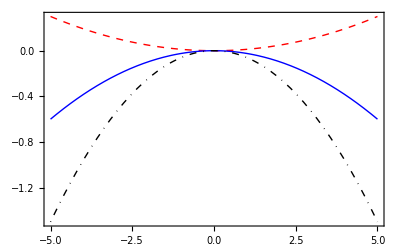

```mathematica
Plot[{ehSph[1,1.2,0.1,π/3,x],ehSph[1,1.2,0.1,π/4,x],ehSph[1,1.2,0.1,π/6,x]},{x,-5,5},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick,Dashed},{Blue,Thick},{Black,DotDashed,Thick}}]
```